# ArrayPlot

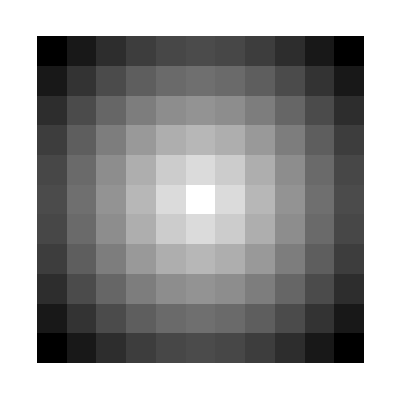

```mathematica
h=10;
data=Table[a+b I,{a,-2,2,4/h},{b,-2,2,4/h}];
ArrayPlot[data]
```

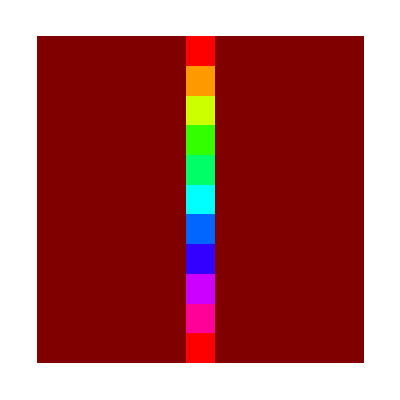

```mathematica
ArrayPlot[data,ColorFunction->Hue]
```

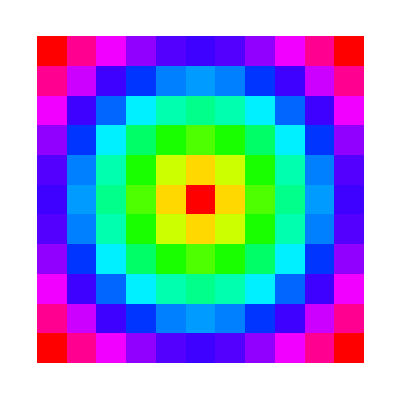

```mathematica
ArrayPlot[Abs[data],ColorFunction->Hue]
```

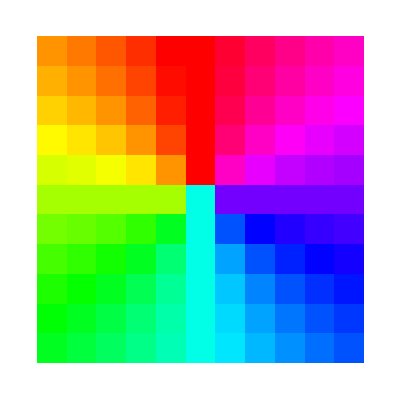

```mathematica
ArrayPlot[Arg[data],ColorFunction->Hue]
```

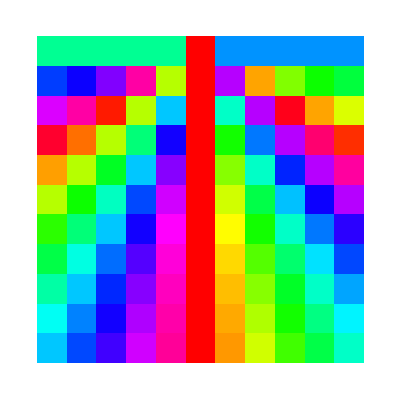

```mathematica
ArrayPlot[data,ColorFunction->(Hue[Arg[#]]&)]
```

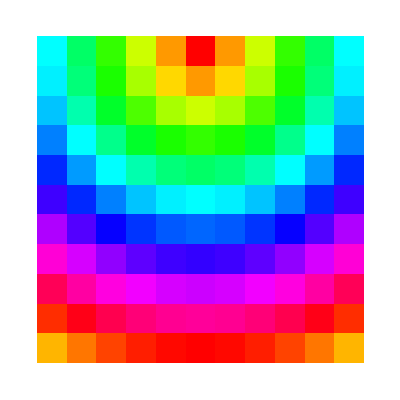

```mathematica
ArrayPlot[data,ColorFunction->(Hue[Abs[#]]&)]
```

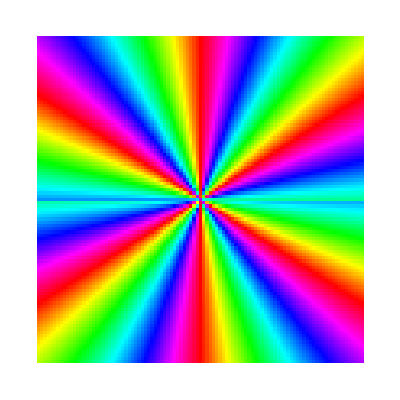

```mathematica
h=100.1;
data=Table[(a+b ⅈ)/(a-b ⅈ),{a,-2,2,4/h},{b,-2,2,4/h}];ArrayPlot[data,ColorFunction->(Hue[Arg[#1]]&)]
```

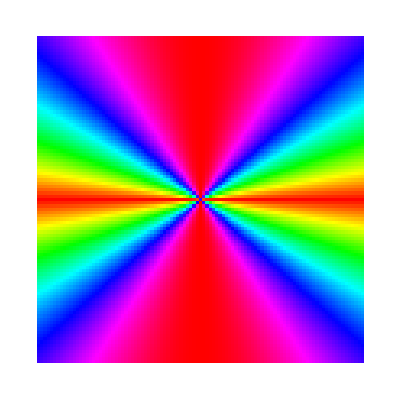

```mathematica
ArrayPlot[data,ColorFunction->(Hue[Abs[#1]]&)]
```

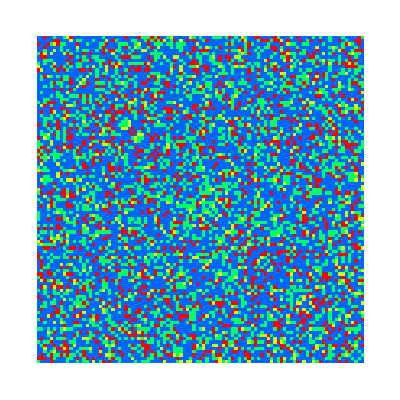

```mathematica
ArrayPlot[Abs[data],ColorFunction->Hue]
```

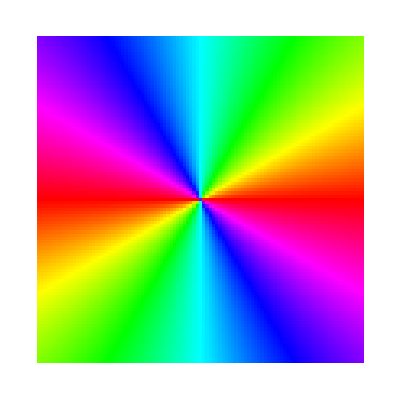

```mathematica
ArrayPlot[Arg[data],ColorFunction->Hue]
```

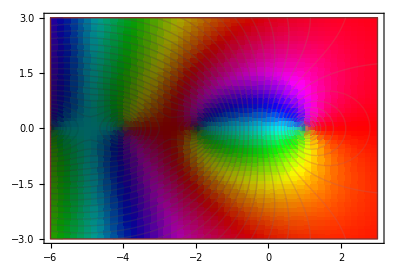

```mathematica
ParametricPlot[(*just need a vis function that will allow x and y to be in the color function*){x, y}, {x, -6, 3}, {y, -3, 3},(*color and mesh functions don't trigger refinement,so just use a big grid*) PlotPoints -> 50, MaxRecursion -> 0, Mesh -> 50,(*turn off scaling so we can do computations with the actual complex values*) ColorFunctionScaling -> False, ColorFunction -> (Hue[(*hue according to argument,with shift so arg(z)==0 is red*)Rescale[Arg[Zeta[# + I #2]], {-Pi, Pi}, {0, 1} + 0.5], 1,(*fudge brightness a bit:0.1 keeps things from getting too dark,2 forces some actual bright areas*) Rescale[Log[Abs[Zeta[# + I #2]]], {-Infinity, Infinity}, {0.1, 2}]]&),(*mesh lines according to magnitude,scaled to avoid the pole at z=1*) MeshFunctions -> {Log[Abs[Zeta[#1 + I #2]]]&},(*turn off axes,because I don't like them with frames*) Axes -> False]
```

```mathematica
ComplexGraph[f_,{xmin_,xmax_},{ymin_,ymax_},opts:OptionsPattern[]]:=RegionPlot[True,{x,xmin,xmax},{y,ymin,ymax},opts,PlotPoints->100,ColorFunctionScaling->False,ColorFunction->Function[{x,y},With[{ff=f[x+I y]},Hue[(2. Pi)^-1 Mod[Arg[ff],2 Pi],1,1-(1.2+10 Log[Abs[ff]+1])^-1]]]]
```

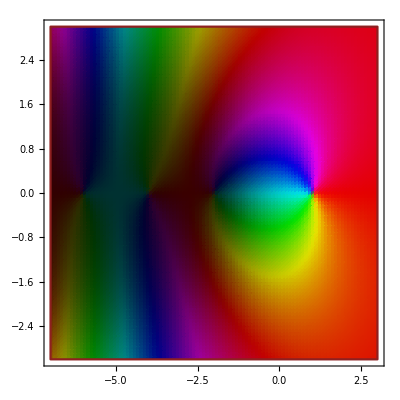

```mathematica
ComplexGraph[Zeta, {-7, 3}, {-3, 3}]
```

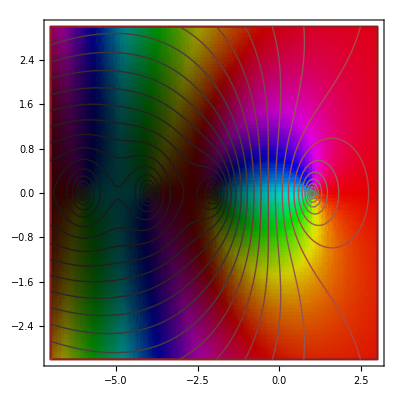

```mathematica
ComplexGraph[Zeta,{-7,3},{-3,3},Mesh->30,MeshFunctions->{Log[Abs[Zeta[#1+I #2]]]&},MeshStyle->{{Thin,Black},None},MaxRecursion->0]
```

```mathematica
Plot3D[
 Log[Abs[Zeta[x + I y]]], {x, -6, 3}, {y, -3, 3},
 (*color and mesh functions don't trigger refinement,so just use a big grid*)
 PlotPoints -> 50, MaxRecursion -> 0, 
 Mesh -> 50, 
 (*turn off scaling so we can do computations with the actual complex values*)
 ColorFunctionScaling -> False, 
 ColorFunction -> (Hue[
     (*hue according to argument,with shift so arg(z)==0 is red*)
     Rescale[Arg[Zeta[# + I #2]], {-Pi, Pi}, {0, 1} + 0.5], 
     1,(*fudge brightness a bit:
     0.1 keeps things from getting too dark,
     2 forces some actual bright areas*)
     Rescale[Log[Abs[Zeta[# + I #2]]], {-Infinity, Infinity}, {0.1, 2}]] &),
     (*mesh lines according to magnitude,scaled to avoid the pole at z=1*)
     MeshFunctions -> {Log[Abs[Zeta[#1 + I #2]]] &},
     (*turn off axes,because I don't like them with frames*)
     Axes -> False]
```

-Graphics3D-